```mathematica
(*note that this places the units of x in mm*)
lambda = 532 * 10^(-6);

ell10 = 5.4;
ell20 = 2;

ne = 1.55332;
no = 1.54422;



alpha = 2*(Pi/180);
phi=0;
theta =(*0 *)Pi/4;
beta =(*Pi/8*)0;


polarization = ({{Cos[theta]}, {Sin[theta]*Exp[I*phi]}});

ell1 = ell10 - x*Tan[alpha];
ell2 = ell20 +x*Tan[alpha];
phi1e= (2*Pi)*ell1*ne/lambda;
phi1o = (2*Pi)*ell1*no/lambda;
phi2e =  (2*Pi)*ell2*ne/lambda;
phi20 =  (2*Pi)*ell2*no/lambda;

w1 = ({{Exp[I*phi1e], 0}, {0, Exp[I*phi1o]}});
w2 =  ({{Exp[I*phi2e], 0}, {0, Exp[I*phi20]}});
r1 = RotationMatrix[-((Pi/4)+beta)];
r2 = RotationMatrix[((Pi/4)+beta)];
```

```mathematica
wedge = FullSimplify[r2.w2.r1.w1];
```

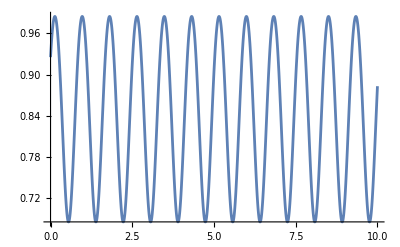

```mathematica
Plot[Abs[(wedge.polarization)[[1,1]]],{x,0,10}]
```

```mathematica
Manipulate[Plot3D[Abs[(wedge.polarization)⟦1,1⟧],{x,0,10},{theta,0,π}],{beta,0,Pi}]
```